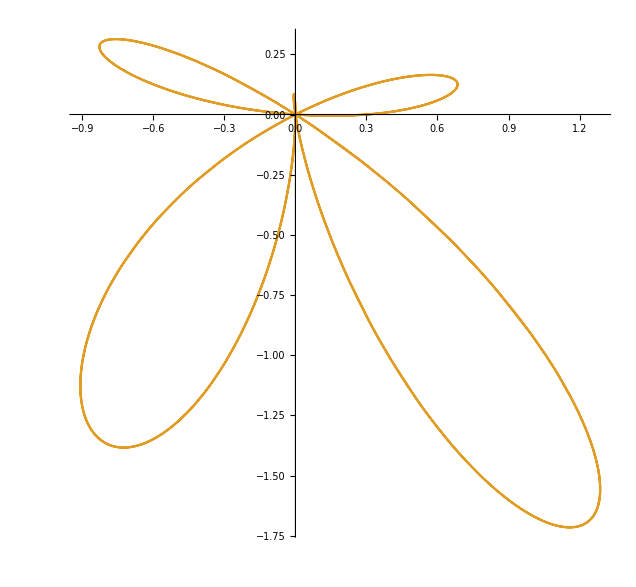

```mathematica
PolarPlot[{0,Sin[5t]+0.3*Cos[7t]-Sin[t]},{t,0,2 Pi}]
(*N[ArcLength[{Sin[t+2]/2+Cos[3*t]/3, t},{t,0,2 Pi},"Polar"]]*)
```

```mathematica
integral=Integrate[(D[a*Sin[b*x]+c*Cos[b*x]+d*Sin[e*x]+f*Cos[e*x], x])^2+(a*Sin[b*x]+c*Cos[b*x]+d*Sin[e*x]+f*Cos[e*x])^2, {x, 0, 2Pi}]
```

1/4 (-2 a b c-2 d e f-(8 b e (b c d-a e f))/((b-e) (b+e))+4 a^2 b^2 π+4 b^2 c^2 π+4 d^2 e^2 π+4 e^2 f^2 π+2 a b c Cos[4 b π]+2 d e f Cos[4 e π]+(8 b e Cos[2 e π] ((b c d-a e f) Cos[2 b π]+(a b d+c e f) Sin[2 b π]))/((b-e) (b+e))+a^2 b Sin[4 b π]-b c^2 Sin[4 b π]-(8 b e ((a d e+b c f) Cos[2 b π]+(-c d e+a b f) Sin[2 b π]) Sin[2 e π])/((b-e) (b+e))+e (d^2-f^2) Sin[4 e π])+1/4 ((2 a c)/b+(2 d f)/e+(8 (-c d e+a b f))/(b^2-e^2)-(2 d f Cos[4 e π])/e+(8 Cos[2 e π] ((c d e-a b f) Cos[2 b π]+(a d e+b c f) Sin[2 b π]))/((b-e) (b+e))+(4 b (a^2+c^2+d^2+f^2) π-2 a c Cos[4 b π]+(-a^2+c^2) Sin[4 b π])/b-(8 ((a b d+c e f) Cos[2 b π]+(-b c d+a e f) Sin[2 b π]) Sin[2 e π])/((b-e) (b+e))+((-d^2+f^2) Sin[4 e π])/e)

```mathematica
1/4 (-2 a b c-2 d e f-(8 b e (b c d-a e f))/((b-e) (b+e))+4 a^2 b^2 π+4 b^2 c^2 π+4 d^2 e^2 π+4 e^2 f^2 π+2 a b c+2 d e f +(8 b e  ((b c d-a e f)))/((b-e) (b+e)))+1/4 ((2 a c)/b+(2 d f)/e+(8 (-c d e+a b f))/(b^2-e^2)-(2 d f)/e+(8 ((c d e-a b f)))/((b-e) (b+e))+(4 b (a^2+c^2+d^2+f^2) π-2 a c)/b)
```

1/4 (4 a^2 b^2 π+4 b^2 c^2 π+4 d^2 e^2 π+4 e^2 f^2 π)+1/4 ((2 a c)/b+(8 (c d e-a b f))/((b-e) (b+e))+(8 (-c d e+a b f))/(b^2-e^2)+(-2 a c+4 b (a^2+c^2+d^2+f^2) π)/b)

```mathematica
Simplify[1/4 (4 a^2 b^2 π+4 b^2 c^2 π+4 d^2 e^2 π+4 e^2 f^2 π)+1/4 ((2 a c)/b+(8 (c d e-a b f))/((b-e) (b+e))+(8 (-c d e+a b f))/(b^2-e^2)+(-2 a c+4 b (a^2+c^2+d^2+f^2) π)/b)]
```

(a^2 (1+b^2)+(1+b^2) c^2+(1+e^2) (d^2+f^2)) π

```mathematica
Expand[(a^2 (1+b^2)+(1+b^2) c^2+(1+e^2) (d^2+f^2)) π]
```

a^2 π+a^2 b^2 π+c^2 π+b^2 c^2 π+d^2 π+d^2 e^2 π+f^2 π+e^2 f^2 π

```mathematica
Integrate[(a*Sin[b*x]+c*Cos[b*x]+d*Sin[e*x]+f*Cos[e*x])^2, {x, 0, 2Pi}]
```

```mathematica
1/4 ((2 a c)/b+(2 d f)/e-(8 (c d e-a b f))/((b-e) (b+e)))+1/4 (-(2 d f)/e+(8  ((c d e-a b f)))/((b-e) (b+e))+(4 b (a^2+c^2+d^2+f^2) π-2 a c)/b)
```

1/4 ((2 a c)/b+(2 d f)/e-(8 (c d e-a b f))/((b-e) (b+e)))+1/4 (-(2 d f)/e+(8 (c d e-a b f))/((b-e) (b+e))+(-2 a c+4 b (a^2+c^2+d^2+f^2) π)/b)

```mathematica
Simplify[1/4 ((2 a c)/b+(2 d f)/e-(8 (c d e-a b f))/((b-e) (b+e)))+1/4 (-(2 d f)/e+(8 (c d e-a b f))/((b-e) (b+e))+(-2 a c+4 b (a^2+c^2+d^2+f^2) π)/b)]
```

(a^2+c^2+d^2+f^2) π